## Threaded operations

### Define the function

```mathematica
myF[a_]:=a*Sin[#]+a*Sin[#]^3/#&;
```

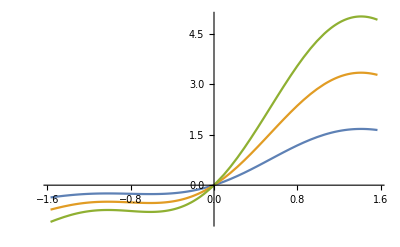

```mathematica
Plot[{myF[1][x],myF[2][x],myF[3][x]},{x,-π/2,π/2}]
```

```mathematica
mpt=MapThread[myF[a],{{x,y,z}}]
```

{a Sin[x]+(a Sin[x]^3)/x,a Sin[y]+(a Sin[y]^3)/y,a Sin[z]+(a Sin[z]^3)/z}